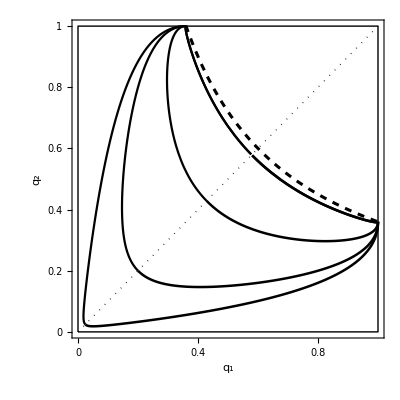

```mathematica
s=.6;

plot1=Show[Table[Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]]],{sp,set={0.05,0.05,0.3,0.5,.59}}],Plot[s^2/x,{x,0,1},PlotStyle->Directive[Thickness[.0055],Black,Dashed]],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dotted,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

```mathematica
Clear[s,sp,t]
theq1=Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2;

theq2=Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2;
theq1P=D[theq1,t]//FullSimplify;
theq2P=D[theq2,t]//FullSimplify;
```

```mathematica
FILL[sps_,spl_,gr_]:=(plotBñ=Show[Table[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},Axes->True,PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{sp,{spl,sps}}]];
{line1,line2}=Cases[plotBñ,l_Line:>First@l,Infinity];
FillB=Graphics[{Opacity[gr],Darker@Gray,Polygon[Join[line1,Reverse@line2]]},Options[plotBñ]];

plotTñ=Show[Table[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},Axes->True,PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{sp,{spl,sps}}]];
{line1,line2}=Cases[plotTñ,l_Line:>First@l,Infinity];

FillT=Graphics[{Opacity[gr],Darker@Gray,Polygon[Join[line1,Reverse@line2]]},Options[plotTñ]];
Show[FillB,FillT])
```

0.45

0.6

0.485

{0.454545,0.548589}

0.292909-0.205486 x

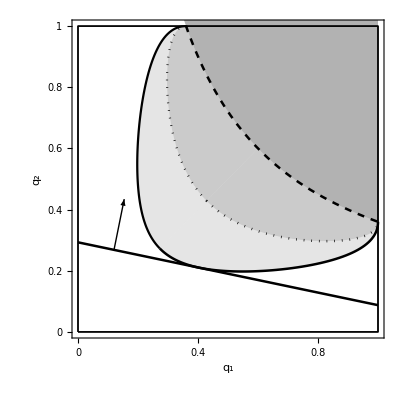

{0.170459,0.829541}

0.24298

Sin[1/2 ArcCos[(s (1-(1-sp) t))/sp]+1/2 ArcCos[(s (1-(1+sp) t))/sp]]^2

Sin[1/2 ArcCos[(s (1-(1-sp) t))/sp]-1/2 ArcCos[(s (1-(1+sp) t))/sp]]^2

1/(2 sp)s ((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))+(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))) Sin[ArcCos[(s (1+(-1+sp) t))/sp]+ArcCos[-(s (-1+t+sp t))/sp]]

-1/(2 sp)s ((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))-(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))) Sin[ArcSin[(s (1+(-1+sp) t))/sp]+ArcSin[(s (-1+t+sp t))/sp]]

```mathematica
s=0.6;
spS=.00001;
spM=.3;
spL=.45;
gray=.3;
top=Plot[s^2/x,{x,0,1},Filling->Top,FillingStyle->Directive[Black,Opacity[.3]],PlotStyle->Directive[Thickness[.0045],Black,Dashed]];

(*****************************************************)

sp=spM;
plotçM=Show[Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black,Dotted],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]]],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]];
(*****************************************************)
(*****************************************************)

sp=spL;
plotçL=Show[Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]]],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]];
(*****************************************************)



sp
s
t=.485
{(1-sp/s)/(1-sp),(1-(sp/s)^2)/(1-sp^2)}
theq2P/theq1P x+(theq2P theq1-theq1P theq2)/-theq1P

rec=Plot[theq2P/theq1P x+(theq2P theq1-theq1P theq2)/-theq1P,{x,0,1},PlotStyle->Directive[Thickness[.0045],Black]];
xa=.12;
lon=.2;arr=Graphics[Arrow[{{xa,theq2P/theq1P xa+(theq2P theq1-theq1P theq2)/-theq1P},{xa+theq2P/(theq2P-theq1P)lon,theq2P/theq1P xa+(theq2P theq1-theq1P theq2)/-theq1P+theq1P/(theq1P-theq2P)lon}}]];

Show[FILL[spS,spM,gray],FILL[spM,spL,gray/2],plotçM,plotçL,top,rec,arr]

{theq2P/(theq2P-theq1P),theq1P/(theq1P-theq2P)}
(theq2P theq1-theq1P theq2)/(theq2P-theq1P)
Clear[s,spL,spS]
```

```mathematica
theq2P/theq1P x+(theq2P theq1-theq1P theq2)/(theq2P-theq1P)//Simplify
```

-((((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))-(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))) x Csc[ArcCos[(s (1+(-1+sp) t))/sp]+ArcCos[-(s (-1+t+sp t))/sp]] Sin[ArcSin[(s (1+(-1+sp) t))/sp]+ArcSin[(s (-1+t+sp t))/sp]])/((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))+(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))))-(-((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))+(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))) Sin[1/2 (ArcCos[(s (1+(-1+sp) t))/sp]-ArcCos[-(s (-1+t+sp t))/sp])]^2 Sin[ArcCos[(s (1+(-1+sp) t))/sp]+ArcCos[-(s (-1+t+sp t))/sp]]-((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))-(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))) Sin[1/2 (ArcCos[(s (1+(-1+sp) t))/sp]+ArcCos[-(s (-1+t+sp t))/sp])]^2 Sin[ArcSin[(s (1+(-1+sp) t))/sp]+ArcSin[(s (-1+t+sp t))/sp]])/(((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))+(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))) Sin[ArcCos[(s (1+(-1+sp) t))/sp]+ArcCos[-(s (-1+t+sp t))/sp]]+((1-sp)/(√(1-(s+s (-1+sp) t)^2/sp^2))-(1+sp)/(√(1-(s^2 (-1+t+sp t)^2)/sp^2))) Sin[ArcSin[(s (1+(-1+sp) t))/sp]+ArcSin[(s (-1+t+sp t))/sp]])

```mathematica
CompX[s_,sp_,t_]:=If[,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2]
```

```mathematica
s=.6;

plot1=Show[Table[Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]-1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2,Sin[1/2 ArcCos[(1-(1+sp)t)/(sp/s)]+1/2 ArcCos[(1-(1-sp)t)/(sp/s)]]^2},{t,(1-sp/s)/(1-sp),Min[1/(1-sp),(1+sp/s)/(1+sp),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]]],{sp,set={0.05,0.05,0.3,0.5,.59}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dotted,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

## 2

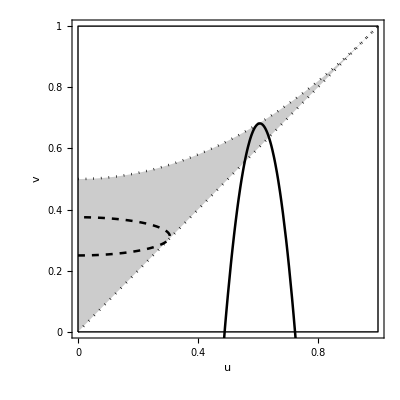

```mathematica
s=.6;
Q=.3;
η1=.4;
Δ=1-2η1;
sp=.1;

plot2=Show[ParametricPlot[{ Q/(√(1-Δ^2)) Cos[θ],Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]},{θ,-π/2,π/2},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dashed],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],
ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2 sp^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],
Plot[{(1+u^2)/2,u},{u,0,1},PlotStyle->Directive[Thickness[.0045],Black,Dotted],Filling-> {1-> {2}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n]
```

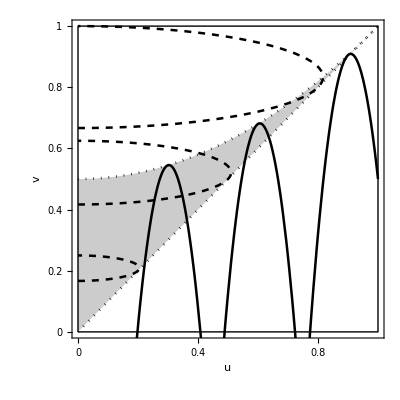

```mathematica
s=.7;
Q=.3;
η1=.4;
Δ=1-2η1;
sp=.1;

plot2=Show[Table[ParametricPlot[{ Q/(√(1-Δ^2)) Cos[θ],Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]},{θ,-π/2,π/2},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dashed],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{Q,{.2,.5,.8}}],
Table[ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2 sp^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{s,{.3,.6,.9}}],
Plot[{(1+u^2)/2,u},{u,0,1},PlotStyle->Directive[Thickness[.0045],Black,Dotted],Filling-> {1-> {2}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n]
```

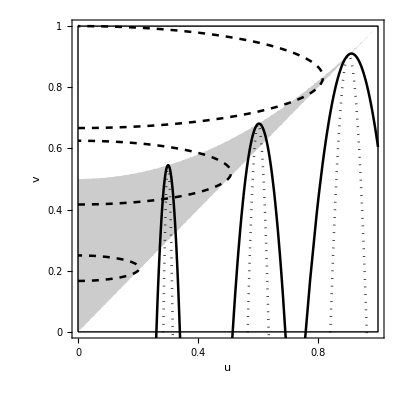

```mathematica
s=.7;
Q=.3;
η1=.4;
Δ=1-2η1;
sp=.1;

plot2=Show[Table[ParametricPlot[{ Q/(√(1-Δ^2)) Cos[θ],Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]},{θ,-π/2,π/2},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dashed],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{Q,{.2,.5,.8}}],
Table[{ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2(s/8)^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2(s/20)^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]]},{s,{.3,.6,.9}}],
Plot[{(1+u^2)/2,u},{u,0,1},PlotStyle->Directive[Thickness[.0001],Black,Dotted],Filling-> {1-> {2}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n]
```

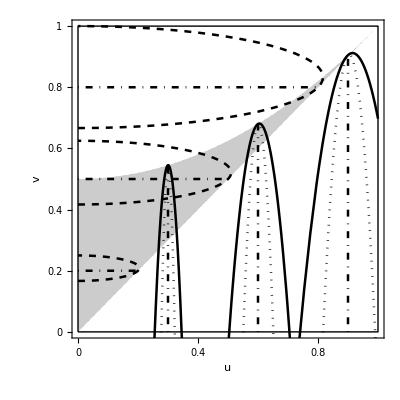

```mathematica
s=.7;
Q=.3;
η1=.4;
Δ=1-2η1;
sp=.1;

plot2=Show[Table[{ParametricPlot[{ Q/(√(1-Δ^2)) Cos[θ],Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]},{θ,-π/2,π/2},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dashed],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],Graphics[{Thickness[.0045],Black,DotDashed,Line[{{0,Q},{Q,Q}}]}]},{Q,{.2,.5,.8}}],
Table[{ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2(s/7)^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2(s/14)^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],
Graphics[{Thickness[.0045],Black,DotDashed,Line[{{s,0},{s,(1+s^2)/2}}]}]},{s,{.3,.6,.9}}],
Plot[{(1+u^2)/2,u},{u,0,1},PlotStyle->Directive[Thickness[.0001],Black,Dotted],Filling-> {1-> {2}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n]
```

```mathematica
eq1=D[Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ],θ]/D[ Q/(√(1-Δ^2)) Cos[θ],θ]//FullSimplify
eq2=D[(1+u^2)/2-(u-s)^2/(2 sp^2),u]/.{u->  Q/(√(1-Δ^2)) Cos[θ],v-> Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]}//FullSimplify
eq3=(1+u^2)/2-(u-s)^2/(2 sp^2)/.{u->  Q/(√(1-Δ^2)) Cos[θ],v-> Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]}//FullSimplify
eq4=v/.{u->  Q/(√(1-Δ^2)) Cos[θ],v-> Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]}//FullSimplify
```

-(Δ Cot[θ])/(√(1-Δ^2))

(s √(1-Δ^2)+Q (-1+sp^2) Cos[θ])/(sp^2 √(1-Δ^2))

1/2 (1+(Q^2 Cos[θ]^2)/(1-Δ^2)-((s-(Q Cos[θ])/(√(1-Δ^2)))^2)/sp^2)

(Q+Q Δ Sin[θ])/(1-Δ^2)

```mathematica
sbz1=eq1-eq2//FullSimplify
sbz2=eq3-eq4//FullSimplify
```

(-s √(1-Δ^2)-Q (-1+sp^2) Cos[θ]-sp^2 Δ Cot[θ])/(sp^2 √(1-Δ^2))

1/2 (1+(Q^2 Cos[θ]^2)/(1-Δ^2)-((s-(Q Cos[θ])/(√(1-Δ^2)))^2)/sp^2+(2 Q (1+Δ Sin[θ]))/(-1+Δ^2))

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

θ==-0.024293&&sp==0.0322031

0.0322031

-0.024293

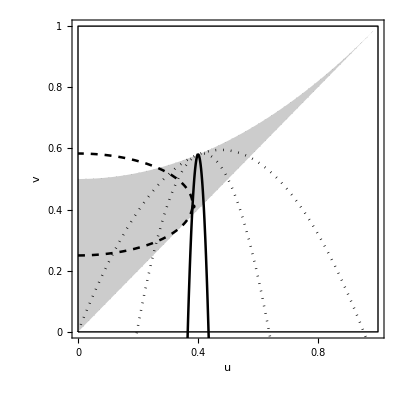

```mathematica
s=.4;
Q=.35;
η1=.3;
Δ=1-2η1;


AA=Reduce[{sbz1==0,sbz2==0,sp≥0,-π/2≤ θ≤ π/2},{θ,sp}]
sp=sp/.ToRules[AA]
theθ=θ/.ToRules[AA]
thepoint=Graphics[{PointSize-> Medium,Point[{ Q/(√(1-Δ^2)) Cos[theθ],Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[theθ]}]}];


plot2=Show[ParametricPlot[{ Q/(√(1-Δ^2)) Cos[θ],Q/(1-Δ^2) +(Q  Δ)/(1-Δ^2) Sin[θ]},{θ,-π/2,π/2},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dashed],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],
ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2 sp^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],
Plot[{(1+u^2)/2,u},{u,0,1},PlotStyle->Directive[Thickness[.0001],Black,Dotted],Filling-> {1-> {2}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],thepoint,
Table[ParametricPlot[{ u,(1+u^2)/2-(u-s)^2/(2 sp^2)},{u,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{u,v},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{sp,{s,s/2}}]]


Clear[s,m,n,Q,η1,Δ,sp]
```

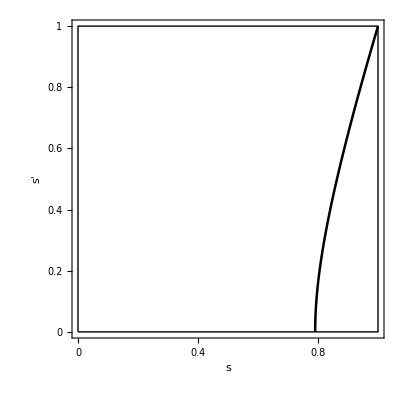

```mathematica
Q=.7;
η1=.2;
Δ=1-2η1;

plot3=Show[ParametricPlot[{ (Q Δ(1+Sin[θ]^2)-(1-Δ^2-2Q)Sin[θ])/(√(1-Δ^2)(Δ+Q Sin[θ])) Sec[θ],-(√((1-Q)^2-(Δ+Q Sin[θ])^2))/(Δ+Q Sin[θ])Tan[θ]},{θ,-ArcSin[Δ],If[Q≥  1-Δ,ArcSin[(1-Q-Δ)/Q],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{"s","s'"},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n]
```

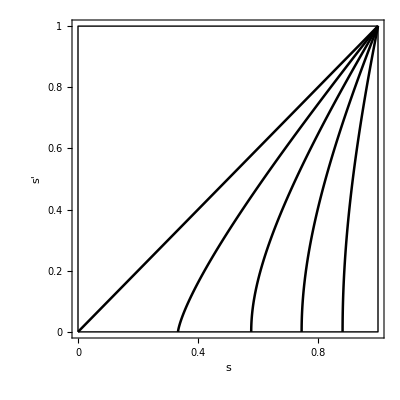

```mathematica
Q=.7;
η1=.1;
Δ=1-2η1;

plot3=Show[Table[ParametricPlot[{ (Q Δ(1+Sin[θ]^2)-(1-Δ^2-2Q)Sin[θ])/(√(1-Δ^2)(Δ+Q Sin[θ])) Sec[θ],-(√((1-Q)^2-(Δ+Q Sin[θ])^2))/(Δ+Q Sin[θ])Tan[θ]},{θ,-ArcSin[Δ],If[Q≥  1-Δ,ArcSin[(1-Q-Δ)/Q],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{s,s'},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{Q,{0,.2,.4,.6,.8}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n]
```

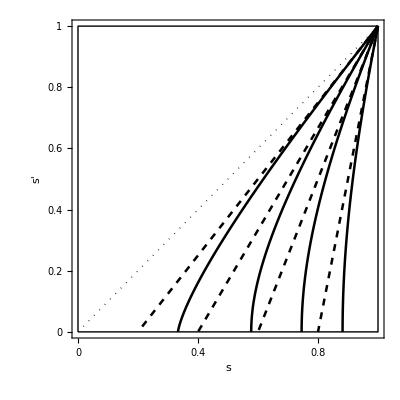

```mathematica
Q=.7;
η1=.1;
Δ=1-2η1;

plot3=Show[Table[ParametricPlot[{ (Q Δ(1+Sin[θ]^2)-(1-Δ^2-2Q)Sin[θ])/(√(1-Δ^2)(Δ+Q Sin[θ])) Sec[θ],-(√((1-Q)^2-(Δ+Q Sin[θ])^2))/(Δ+Q Sin[θ])Tan[θ]},{θ,-ArcSin[Δ],If[Q≥  1-Δ,ArcSin[(1-Q-Δ)/Q],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{s,s'},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{Q,{.2,.4,.6,.8}}],Table[Δ=10^-3;ParametricPlot[{ (Q Δ(1+Sin[θ]^2)-(1-Δ^2-2Q)Sin[θ])/(√(1-Δ^2)(Δ+Q Sin[θ])) Sec[θ],-(√((1-Q)^2-(Δ+Q Sin[θ])^2))/(Δ+Q Sin[θ])Tan[θ]},{θ,-ArcSin[Δ],If[Q≥  1-Δ,ArcSin[(1-Q-Δ)/Q],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dashed],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{s,s'},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{Q,{.2,.4,.6,.8}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],
Graphics[{Dotted,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n,Q,η1,Δ,sp]
```

```mathematica
Solve[-(√((1-Q)^2-(Δ+Q si)^2))/(Δ+Q  si)si/(√(1-si^2))==1,si]
```

{{si→-Δ},{si→-Δ/(-1+2 Q)}}

```mathematica
Solve[(Q Δ(1+si^2)-(1-Δ^2-2Q)si)/(√(1-Δ^2)(Δ+Q si)) 1/(√(1-si^2))==1,si]
```

$Aborted

```mathematica
(Q Δ(1+si^2)-(1-Δ^2-2Q)si)/(√(1-Δ^2)(Δ+Q si)) 1/(√(1-si^2))/. si->-Δ//FullSimplify
```

1

```mathematica
(Q Δ(1+si^2)-(1-Δ^2-2Q)si)/(√(1-Δ^2)(Δ+Q si)) 1/(√(1-si^2))/. si->(1-Q-Δ)/Q//FullSimplify
```

(Q √(-((-1+Δ) (-1+2 Q+Δ))/Q^2))/(√(1-Δ^2))

```mathematica
√((-1+2 Q+Δ)/(1+Δ))
```

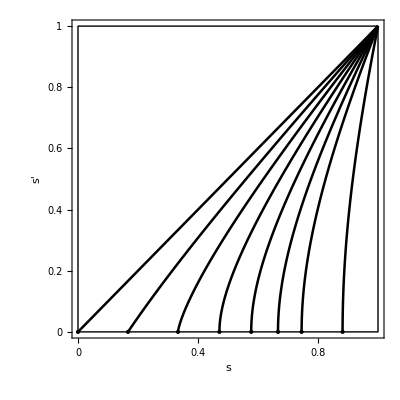

```mathematica
Q=.7;
η1=.1;
Δ=1-2η1;



plot3=Show[Table[Show[ParametricPlot[{ (Q Δ(1+Sin[θ]^2)-(1-Δ^2-2Q)Sin[θ])/(√(1-Δ^2)(Δ+Q Sin[θ])) Sec[θ],-(√((1-Q)^2-(Δ+Q Sin[θ])^2))/(Δ+Q Sin[θ])Tan[θ]},{θ,-ArcSin[Δ],If[Q≥  1-Δ,ArcSin[(1-Q-Δ)/Q],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{s,s'},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],Graphics[{PointSize->   Large,Point[{If[Q≤ 2η1,Q/(2 √(η1(1-η1))),√((Q-η1)/(1-η1))],0}]}]],{Q,{0,0.1,.2,0.3,.4,0.5,.6,.8}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n]
```

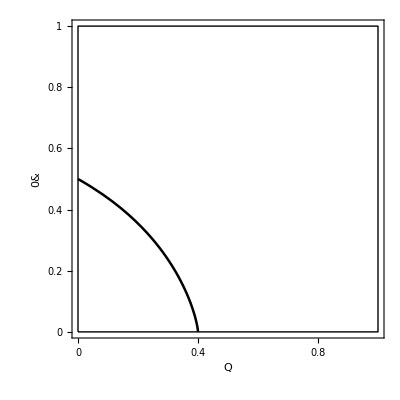

```mathematica
η1=.2;
Δ=1-2η1;
s=.5;

plot3=Show[ParametricPlot[{thesp2=√(1-Δ^2) (√(1-Δ^2)(1+s^2)Cos[θ]-2s(1+Δ Sin[θ]))/(Δ+Sin[θ])^2 Sin[θ]^2 Sec[θ];(s √(1-Δ^2)+thesp2 Δ Cot[θ])/((1-thesp2) Cos[θ]),√thesp2},{θ,-ArcTan[(s Δ)/(√(1-Δ^2))],If[η1≤  s^2/(1+s^2),-ArcCos[(2s √(1-Δ^2))/(1-Δ+s^2(1+Δ))],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Q,s'},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n,Q,η1,Δ,sp]
```

0.4

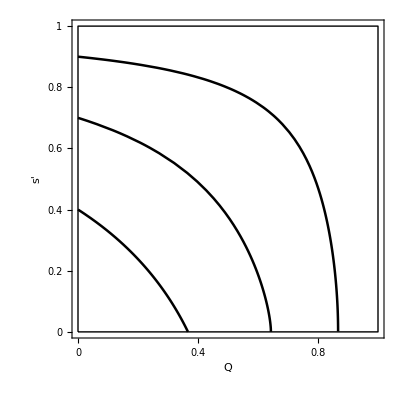

```mathematica
η1=.3;
Δ=1-2η1


plot3=Show[Table[ParametricPlot[{thesp2=√(1-Δ^2) (√(1-Δ^2)(1+s^2)Cos[θ]-2s(1+Δ Sin[θ]))/(Δ+Sin[θ])^2 Sin[θ]^2 Sec[θ];(s √(1-Δ^2)+thesp2 Δ Cot[θ])/((1-thesp2) Cos[θ]),√thesp2},{θ,-ArcTan[(s Δ)/(√(1-Δ^2))],If[η1≤  s^2/(1+s^2),-ArcCos[(2s √(1-Δ^2))/(1-Δ+s^2(1+Δ))],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Q,"s'"},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{s,{.4,.7,.9}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n,Q,η1,Δ,sp]
```

```mathematica
ParametricPlot[{Q,If[Q≤ s,(s-Q)/(1-Q),0]},{Q,0,1}]
```

0.8

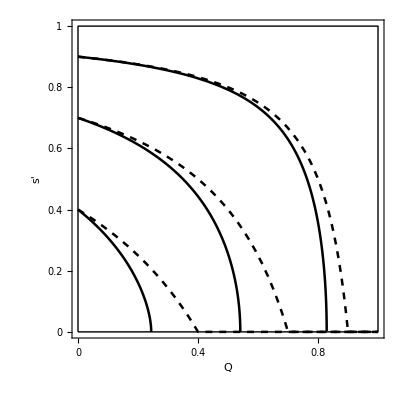

```mathematica
η1=.1;
Δ=1-2η1


plot3=Show[Table[Show[ParametricPlot[{thesp2=√(1-Δ^2) (√(1-Δ^2)(1+s^2)Cos[θ]-2s(1+Δ Sin[θ]))/(Δ+Sin[θ])^2 Sin[θ]^2 Sec[θ];(s √(1-Δ^2)+thesp2 Δ Cot[θ])/((1-thesp2) Cos[θ]),√thesp2},{θ,-ArcTan[(s Δ)/(√(1-Δ^2))],If[η1≤  s^2/(1+s^2),-ArcCos[(2s √(1-Δ^2))/(1-Δ+s^2(1+Δ))],0]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Q,"s'"},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],
ParametricPlot[{Q,If[Q≤ s,(s-Q)/(1-Q),0]},{Q,0,1},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dashed],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Q,"s'"},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]]
],{s,{.4,.7,.9}}]
,Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]


Clear[s,m,n,Q,η1,Δ,sp]
```

```mathematica
Clear[s,sp]
FullSimplify[({{√((1-s)/(1-sp)), 0, -√((s-sp)/(1-sp))}, {0, 1, 0}, {√((s-sp)/(1-sp)), 0, √((1-s)/(1-sp))}}).({{1, 0, 0}, {0, √((1+sp)/(1+s)), -√((s-sp)/(1+s))}, {0, √((s-sp)/(1+s)), √((1+s')/(1+s))}}),0<sp<s<1]//FullSimplify//MatrixForm
({{√((-1+s)/(-1+sp)), (-s+sp)/(√(-(1+s) (-1+sp))), -√(((-s+sp) (1+s'))/((1+s) (-1+sp)))}, {0, √((1+sp)/(1+s)), -√((s-sp)/(1+s))}, {√((-s+sp)/(-1+sp)), √(((-1+s) (s-sp))/((1+s) (-1+sp))), √(((-1+s) (1+s'))/((1+s) (-1+sp)))}})
```